```mathematica
Clear["Global`*"]
```

#### Constants & Initial Conditions

```mathematica
(*Genaral Constants*)
G=6.67430 10^-11 (*Nm^2/kg^2*);
c=2.99792458 10^8 (*m/s*);
α=1/137.0359992 (*Dimensionless*);
mH= 1.674 10^-27(*kg*);
T0=2.725 (*K*);
kB=1.38064852 10^-23 (*J/K*);
me=9.109 10^-31 (*kg*);
ℏ=1.054571817 10^-34 (*Js*);
ϵ0=2.179 10^-18 (*J*);
Yp=0.;
H0=2.2685455 10^-18 (*1/s*);
σ=6.6524587158 10^-29 (*m2*);
```

```mathematica
(*Saha Parameters*)
a=Exp[x];
Tb=T0/a (*K*);
Ωb0=0.05;
nbSaha=(1-Yp)(3 H0^2 Ωb0)/(8π G mH a^3);
```

```mathematica
(*Cosmology Parameters*)
Neff=3.046;
Ωcdm0=0.267;
Ωk0=0;
Ωγ0=2 π^2/30(kB T0)^4/(ℏ^3 c^5)(8π G)/(3 H0^2);
Ων0=Neff 7/8(4/11)^(4/3)Ωγ0;
ΩΛ0=1-(Ωk0+Ωb0+Ωcdm0+Ωγ0+Ων0);
```

```mathematica
(*Hubble Parameter*)
A=Exp[X];
TB=T0/A;
H=H0 √((Ωb0+Ωcdm0)A^-3+(Ωγ0+Ων0)A^-4+Ωk0 A^-2+ΩΛ0);
```

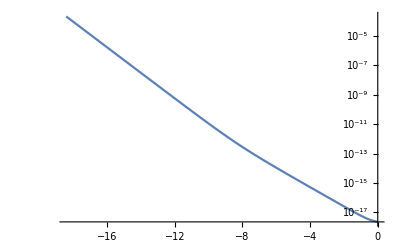

```mathematica
LogPlot[H,{X,xStart,xEnd},PlotRange->All]
```

```mathematica
(*Peebles Parameters*)
Cr=(Λ2s+Λα)/(Λ2s+Λα+β2) (*Dimensionless*);
Λ2s=8.227 (*1/s*);
Λα=H(3ϵ0)^3/((8π)^2 c^3 ℏ^3 n1s) (*1/s*);
n1s=(1-Xe[X])nH (*1/m3*);
nH=(1-Yp)nbPeebles (*1/m3*);
nbPeebles=(1-Yp)(3 H0^2 Ωb0)/(8π G mH A^3)(*1/m3*);
β2=β Exp[(3ϵ0)/(4kB TB)] (*1/s*);
β=α2((me kB TB)/(2π ℏ^2))^(3/2)Exp[-ϵ0/(kB TB)] (*1/s*);
α2=8/(√(3π))c σ √(ϵ0/(kB TB))ϕ2 (*m3/s*);
ϕ2=0.448Log[ϵ0/(kB TB)];
```

```mathematica
(*Interval*)
xStart=Log[10^-8];
xEnd=Log[1.];
n=1000;
x=Table[i,{i,xStart,xEnd,(xEnd-xStart)/(n-1)}];
```

#### Solution Saha Equation

```mathematica
(*Saha Factor*)
Saha=Chop[1/nbSaha((me kB Tb)/(2π ℏ^2))^(3/2)Exp[-ϵ0/(kB Tb)]];
```

{4.48216,Null}

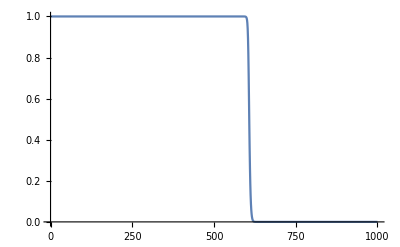

```mathematica
(*Saha Equation*)
Timing[S=Table[Quiet@Solve[Xe^2/(1-Xe)-Saha[[i]]==0,Xe][[2]],{i,n}];]
ListLinePlot[Xe/.S]
```

#### Solution Saha-Peebles Equation

```mathematica
(*Saha Limit & Settings*)
l=0.99;
m=Count[Xe/.S,u_/;u>l];
xmin=x[[m]];
Xe0=Xe/.S[[m]];
```

```mathematica
(*Peebles Equation*)
P=NDSolve[{Xe'[X]==Cr/H(β(1-Xe[X])-nH α2 Xe[X]^2),Xe[xmin]==Xe0},Xe,{X,xmin,xEnd}]
```

{{Xe→InterpolatingFunction[{{-7.37565, 0.}}, <>]}}

#### Plot of the Solution

```mathematica
PeeblesSolution=Piecewise[{{Interpolation[Table[{x[[i]],Xe/.S[[i]]},{i,m}]][X],xStart≤X≤xmin},{Evaluate[Xe[X]/.P][[1]],xmin<X≤xEnd}}];
SahaSolution=Interpolation[Table[{x[[i]],Xe/.S[[i]]},{i,n}]][X];
```

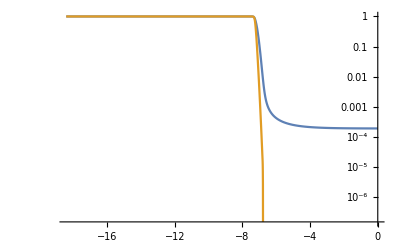

```mathematica
LogPlot[{PeeblesSolution,SahaSolution},{X,xStart,xEnd},PlotRange->All]
```

#### Optical Depth

```mathematica
(*τ ODE*)
ne = nbPeebles PeeblesSolution;
T=NDSolve[{τ'[X]==-(c σ PiecewiseExpand[ne, xStart≤X≤xEnd])/H ,τ[xEnd]==0.},τ,{X,xStart,xEnd}]
```

{{τ→InterpolatingFunction[{{-18.4207, 0.}}, <>]}}

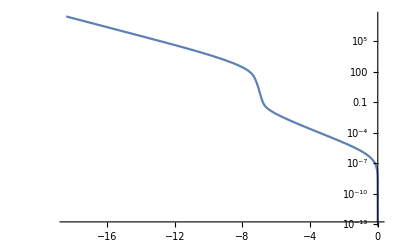

```mathematica
LogPlot[Evaluate[τ[y]/.T],{y,xStart,xEnd},PlotRange->All]
```